# Setup

## General

```mathematica
Get["DiFfRG`"]
SetDirectory[GetDirectory[]];
DefineFormExecutable["/usr/bin/tform -w16"]
```

Mathematica package DiFfRG loaded
Authors: Franz Richard Sattler
Version: 2.0
Year: 2025

Welcome to  █▀ ▐▄█ █▚▌ ▐◀ █ ▀█▀
Author: Franz Richard Sattler
Version: 0.2.1
Year: 2025
For more information and a brief introduction to the package, call FInfo[].
To run the testing suite, you can call  FTest[].

DiFfRG Flow output directory is set to /mnt/data/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows
	This can be modified by using SetFlowName["YourNewName"]

TFORM 4.3.1 (Apr 11 2023, v4.3.1) 64-bits

## Defining the theory

```mathematica
fields= <|
"Commuting"-> {A[p,{v, c}]},
"Grassmann"->{{cb[p,{c}],c[p,{c}]}}
|>;
```

```mathematica
truncation=<|
GammaN->{{A,A},{A,A,A},{A,A,A,A},{A,cb,c},{cb,c}},
Propagator->{{A,A},{cb,c}},Rdot->{{A,A},{cb,c}},
S->{{A,A},{A,A,A},{A,A,A,A},{cb,c},{cb,c,A}},
Field->{{}}
|>;
```

```mathematica
bases=<|
GammaN->{{A,A}->{"AA",1},{A,A,A}->"AAAClass",{A,A,A,A}->"AAAAClass",{A,cb,c}->{"Acbc",1},{cb,c}->"cbc"},
S->{{A,A}->{"AA",1},{A,A,A}->"AAAClass",{A,A,A,A}->"AAAAClass",{A,cb,c}->{"Acbc",1},{cb,c}->"cbc"},
Propagator->{{A,A}->{"AA",1},{cb,c}->"cbc"},
Rdot->{{A,A}->{"AA",1},{cb,c}->"cbc"}
|>;
```

```mathematica
diagramStyling=<|"Styles"->{A->{Orange},c->{Black,Dashed}}|>;
SetTexStyles[cb->"\\bar{c}"];
```

```mathematica
Setup=<|
"FieldSpace"->fields,
"Truncation"->truncation,
"FeynmanRules"->bases,
"DiagramStyling"->diagramStyling
|>;
FSetGlobalSetup[Setup];
```

## Feynman rules

### Momentum configurations

```mathematica
SP3Patt[p1e_,p2e_,p3e_]:={√((sp[p1,p1]+sp[p2,p2]+sp[p3,p3])/3)}/.{p1:>p1e,p2:>p2e,p3:>p3e}//UseLorentzLinearity//FullSimplify;
SP4Patt[p1e_,p2e_,p3e_,p4e_]:={√((sp[p1,p1]+sp[p2,p2]+sp[p3,p3]+sp[p4,p4])/4)}/.{p1:>p1e,p2:>p2e,p3:>p3e,p4:>p4e}//UseLorentzLinearity//FullSimplify;
```

### Rules

```mathematica
dressingRules=ReplaceRepeated[#,{
dressing[GammaN,{cb,c},1,{p1_,p2_}]:>-Zc[√sp[p2,p2]]sp[p2,p2],
dressing[GammaN,{A,A},1,{p1_,p2_}]:>ZA[√sp[p2,p2]]sp[p2,p2],

dressing[InverseProp,{cb,c},1,{p1_,p2_}]:>-(Zc[√sp[p2,p2]]sp[p2,p2]+RB[k^2,sp[p2,p2]]Zc[k]),
dressing[InverseProp,{A,A},1,{p1_,p2_}]:>ZA[√sp[p2,p2]]sp[p2,p2]+RB[k^2,sp[p2,p2]]ZA[evP],

dressing[GammaN,{A,cb,c},1,{p1_,p2_,p3_}]:>ZAcbc[p1,p2], 
dressing[GammaN,{A,A,A},1,{p1_,p2_,p3_}]:>ZA3[p1,p2], 
dressing[GammaN,{A,A,A,A},1,{p1_,p2_,p3_,p4_}]:>ZA4[p1,p2,p3] ,

ZAcbc[p1_,p2_]:>ZAcbc@@SP3Patt[p1,p2,-p1-p2],
ZA3[p1_,p2_]:>ZA3@@SP3Patt[p1,p2,-p1-p2],
ZA4[p1_,p2_,p3_]:>ZA4@@SP4Patt[p1,p2,p3,-p1-p2-p3],

nZA->6,
evP:>(k^nZA+1)^(1/nZA),
devP:>k^(-1+nZA) (1+k^nZA)^(-1+1/nZA),
dressing[Rdot,{A,A},1,{p1_,p2_}]:>ZA[evP]RBdot[k^2,sp[p2,p2]]+RB[k^2,sp[p2,p2]](dtZA[evP]+k*devP*(ZA[1.02evP]-ZA[evP])/(0.02*evP)),
dressing[Rdot,{cb,c},1,{p1_,p2_}]:>Zc[k]RBdot[k^2,sp[p2,p2]]+RB[k^2,sp[p2,p2]](dtZc[k]+k(Zc[1.02*k]-Zc[k])/(0.02*k))
}]&;

FSetSymmetricDressing[GammaN,{A,A}]
```

### Parametrizations

```mathematica
PropParam[expr_]:=UseLorentzLinearity[expr]//.{
lf1->l1,(*We don't care about this in vacuum*)
sp[p1,p1]->p^2,sp[l1,l1]->l1^2,
sp[l1,p1]->l1 p cos[p,l1],
sp[p1,l1]->l1 p cos[p,l1],
√(a_^2):>a,(a_^2)^(n_/2):>a^n,
cos[l1,p]:>cos1
};

SP3FormRule=FMakeSPFormRule[{l1,lf1},p,{p1,p2,p3}];
SP4FormRule=FMakeSPFormRule[{l1,lf1},p,{p1,p2,p3,p4}];
SPParam[expr_]:=UseLorentzLinearity[expr]//.{
lf1->l1,(*We don't care about this in vacuum*)
sp[p,p]->p^2,sp[l1,l1]->l1^2,
sp[l1,p1]->p l1 cos[l1,p1],
sp[l1,p2]->p l1 cos[l1,p2],
sp[l1,p3]->p l1 cos[l1,p3],
sp[l1,p4]->p l1 cos[l1,p4],

√(a_^2):>a,(a_^2)^(n_/2):>a^n,(a_^2)^(n_/2):>a^n,Power[Power[l1_,2],Rational[n_,2]]:>l1^n,
cos[l1,p1]:>cosl1p1,
cos[l1,p2]:>cosl1p2,
cos[l1,p3]:>cosl1p3,
cos[l1,p4]:>cosl1p4
};

SetNc[3]
$Assumptions=k>0&&p>0&&l1>0&&-1<cos1<1&&-1<cos2<1&&-1<cos3<1;
```

## Code Generation

```mathematica
interpolatorType="SplineInterpolator1D<double, LogarithmicCoordinates1D<double>, GPU_memory>";

kernelParameterList={
<|"Name"->"k","Type"->"double"|>,
(*strong couplings*)
<|"Name"->"ZA3","Type"->interpolatorType,"Const"->True,"Reference"->True|>,
<|"Name"->"ZAcbc","Type"->interpolatorType,"Const"->True,"Reference"->True|>,
<|"Name"->"ZA4","Type"->interpolatorType,"Const"->True,"Reference"->True|>,
(*ghost propagator*)
<|"Name"->"dtZc","Type"->interpolatorType,"Const"->True,"Reference"->True|>,
<|"Name"->"Zc","Type"->interpolatorType,"Const"->True,"Reference"->True|>,
(*glue propagator*)
<|"Name"->"dtZA","Type"->interpolatorType,"Const"->True,"Reference"->True|>,
<|"Name"->"ZA","Type"->interpolatorType,"Const"->True,"Reference"->True|>
};

SP4Defs=DeclareSymmetricPoints4DP4[l1,p,{p1,p2,p3,p4}];
SP3Defs=DeclareSymmetricPoints4DP3[l1,p,{p1,p2,p3}];
```

# Flows

```mathematica
FSetCacheDirectory[NotebookDirectory[]<>"/TraceCache/"]
```

```mathematica
FSetRegisterSize[64]
```

## Propagators

## Gluon propagator


-Graphics-+-Graphics--Graphics-+-Graphics--Graphics-

-Graphics-

/mnt/data/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/ZA/ZA.hh unchanged

/mnt/data/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/ZA/kernel.hh unchanged

/mnt/data/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/ZA/src/constructor.cc unchanged

/mnt/data/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/ZA/src/CT_get.cc unchanged

/mnt/data/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/ZA/src/CT_map_1.cc unchanged

Please run UpdateFlows[] to export an up-to-date CMakeLists.txt

Exported to "/mnt/data/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/CMakeLists.txt"

/mnt/data/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/flows.hh unchanged

/mnt/data/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/flows.cc unchanged

```mathematica
fRGAA=FTakeDerivatives[WetterichEquation,{A[i1],A[i2]}]//FTruncate//FPlot//FRoute//FPrint;

traceExprAA=FTerm[TBGetProjector["AA",1,{i1,i2}/.fRGAA["1-Loop"]["ExternalIndices"]]]**(fRGAA["1-Loop"]["Expression"]/.FMakeDiagrammaticRules[]);
FlowAA=FormTrace[traceExprAA]//dressingRules//PropParam//Simplify;

MakeKernel[FlowAA/p^2,

"Name"->"ZA",
"Integrator"->"Integrator_p2_1ang",
"d"->4,
"AD"->False,
"ctype"->"double",
"Device"->"GPU",
"Type"->"double",

"Parameters"->kernelParameterList,
"IntegrationVariables"->{"l1","cos1"},
"Coordinates"->{"LogarithmicCoordinates1D<double>"},
"CoordinateArguments"->{"p"}]
UpdateFlows["YangMillsFlows"]
```

## Ghost propagator

```mathematica
fRGcbc=FTakeDerivatives[WetterichEquation,{cb[i1],c[i2]}]//FTruncate//FPlot//FRoute//FPrint;

traceExprcbc=FTerm[TBGetProjector["cbc",1,{i1,i2}/.fRGcbc["1-Loop"]["ExternalIndices"]]]**(fRGcbc["1-Loop"]["Expression"]/.FMakeDiagrammaticRules[]);
Flowcbc=FormTrace[traceExprcbc]//dressingRules//PropParam//Simplify;

MakeKernel[-Flowcbc/p^2,

"Name"->"Zc",
"Integrator"->"Integrator_p2_1ang",
"d"->4,
"AD"->False,
"ctype"->"double",
"Device"->"GPU",
"Type"->"double",

"Parameters"->kernelParameterList,
"IntegrationVariables"->{"l1","cos1"},
"Coordinates"->{"LogarithmicCoordinates1D<double>"},
"CoordinateArguments"->{"p"}]
UpdateFlows["YangMillsFlows"]
```

-Graphics--Graphics-+-Graphics--Graphics-

-Graphics-

/mnt/data/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/Zc/Zc.hh unchanged

/mnt/data/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/Zc/kernel.hh unchanged

/mnt/data/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/Zc/src/constructor.cc unchanged

/mnt/data/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/Zc/src/CT_get.cc unchanged

/mnt/data/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/Zc/src/CT_map_1.cc unchanged

Please run UpdateFlows[] to export an up-to-date CMakeLists.txt

Exported to "/mnt/data/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/CMakeLists.txt"

/mnt/data/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/flows.hh unchanged

/mnt/data/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/flows.cc unchanged

## Strong couplings

## Ghost-Gluon Vertex

-Graphics-+-Graphics-+-Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-

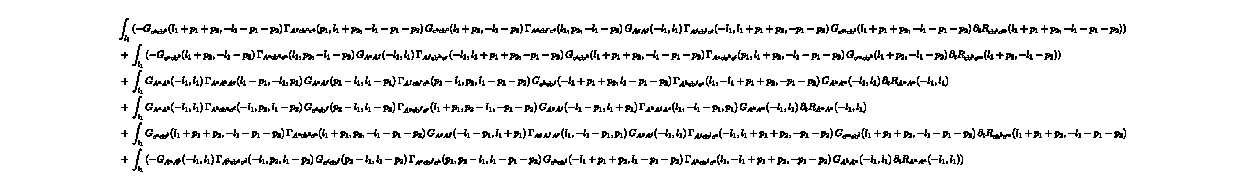

/mnt/data/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/ZAcbc/ZAcbc.hh unchanged

/mnt/data/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/ZAcbc/kernel.hh unchanged

/mnt/data/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/ZAcbc/src/constructor.cc unchanged

/mnt/data/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/ZAcbc/src/CT_get.cc unchanged

/mnt/data/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/ZAcbc/src/CT_map_1.cc unchanged

Please run UpdateFlows[] to export an up-to-date CMakeLists.txt

Exported to "/mnt/data/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/CMakeLists.txt"

/mnt/data/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/flows.hh unchanged

/mnt/data/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/flows.cc unchanged

```mathematica
fRGAcbc=FTakeDerivatives[WetterichEquation,{A[i1],cb[i2],c[i3]}]//FTruncate//FSimplify//FPlot//FRoute//FPrint;

projectorAcbc=FTerm[TBGetProjector["Acbc",1,{i1,i2,i3}/.fRGAcbc["1-Loop"]["ExternalIndices"]]];
traceExprAcbc=projectorAcbc**(fRGAcbc["1-Loop"]["Expression"]/.FMakeDiagrammaticRules[]);

FlowAcbc=FormTrace[traceExprAcbc,{},SP3FormRule]//dressingRules//TBProjectToSymmetricPoint[#,l1,p,p1,p2,p3]&//SPParam//Simplify;

MakeKernel[FlowAcbc,

"Name"->"ZAcbc",
"Integrator"->"Integrator_p2_4D_2ang",
"d"->4,
"AD"->False,
"ctype"->"double",
"Device"->"GPU",
"Type"->"double",

"Parameters"->kernelParameterList,
"KernelBody"->SP3Defs,
"IntegrationVariables"->{"l1","cos1","cos2"},
"Coordinates"->{"LogarithmicCoordinates1D<double>"},
"CoordinateArguments"->{"p"}]
UpdateFlows["YangMillsFlows"]
```

## Three-Gluon Vertex

```mathematica
fRGA3=FTakeDerivatives[WetterichEquation,{A[i1],A[i2],A[i3]}]//FTruncate//FPlot//FRoute//FPrint;

projectorA3=FTerm[TBGetProjector["AAAClassTrans",1,{i1,i2,i3}/.fRGA3["1-Loop"]["ExternalIndices"]]]//TBProjectToSymmetricPoint[#,l1,p,p1,p2,p3]&//Simplify;
traceExprA3=projectorA3**(fRGA3["1-Loop"]["Expression"]/.FMakeDiagrammaticRules[]);
FlowA3=FormTrace["ZA3",traceExprA3,{},SP3FormRule]//dressingRules//TBProjectToSymmetricPoint[#,l1,p,p1,p2,p3]&//SPParam//Simplify;

MakeKernel[FlowA3,

"Name"->"ZA3",
"Integrator"->"Integrator_p2_4D_2ang",
"d"->4,
"AD"->False,
"ctype"->"double",
"Device"->"GPU",
"Type"->"double",

"Parameters"->kernelParameterList,
"KernelBody"->SP3Defs,
"IntegrationVariables"->{"l1","cos1","cos2"},
"Coordinates"->{"LogarithmicCoordinates1D<double>"},
"CoordinateArguments"->{"p"}]
UpdateFlows["YangMillsFlows"]
```

-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-

-Graphics-

/mnt/data/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/ZA3/ZA3.hh unchanged

/mnt/data/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/ZA3/kernel.hh unchanged

/mnt/data/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/ZA3/src/constructor.cc unchanged

/mnt/data/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/ZA3/src/CT_get.cc unchanged

/mnt/data/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/ZA3/src/CT_map_1.cc unchanged

Please run UpdateFlows[] to export an up-to-date CMakeLists.txt

Exported to "/mnt/data/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/CMakeLists.txt"

/mnt/data/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/flows.hh unchanged

/mnt/data/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/flows.cc unchanged

## Four-Gluon Vertex

-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-

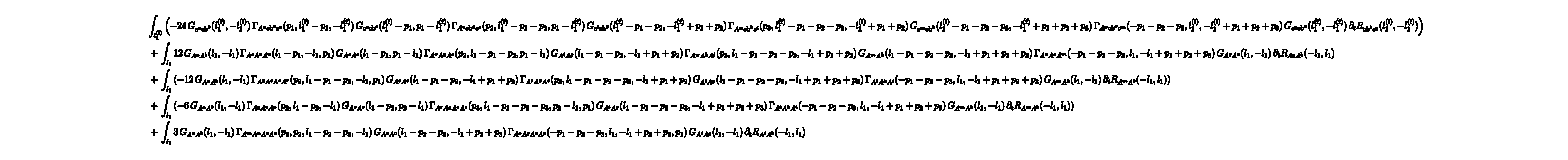

/mnt/data/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/ZA4/ZA4.hh unchanged

/mnt/data/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/ZA4/kernel.hh unchanged

/mnt/data/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/ZA4/src/constructor.cc unchanged

/mnt/data/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/ZA4/src/CT_get.cc unchanged

/mnt/data/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/ZA4/src/CT_map_1.cc unchanged

Please run UpdateFlows[] to export an up-to-date CMakeLists.txt

Exported to "/mnt/data/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/CMakeLists.txt"

/mnt/data/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/flows.hh unchanged

/mnt/data/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/flows.cc unchanged

```mathematica
fRGA4=FTakeDerivatives[WetterichEquation,{A[i1],A[i2],A[i3],A[i4]}]//FTruncate//FPlot//FRoute//FPrint;

projectorA4=FTerm[TBGetProjector["AAAAClassTrans",1,{i1,i2,i3,i4}/.fRGA4["1-Loop"]["ExternalIndices"]]]//TBProjectToSymmetricPoint[#,l1,p,p1,p2,p3,p4]&//Simplify;
traceExprA4=projectorA4**(fRGA4["1-Loop"]["Expression"]/.FMakeDiagrammaticRules[])//TBProjectToSymmetricPoint[#,l1,p,p1,p2,p3,p4]&;
FlowA4=FormTrace["ZA4",traceExprA4,{},SP4FormRule]//dressingRules//TBProjectToSymmetricPoint[#,l1,p,p1,p2,p3,p4]&//SPParam//Simplify;

MakeKernel[FlowA4,

"Name"->"ZA4",
"Integrator"->"Integrator_p2_4D_3ang",
"d"->4,
"AD"->False,
"ctype"->"double",
"Device"->"GPU",
"Type"->"double",

"Parameters"->kernelParameterList,
"KernelBody"->SP4Defs,
"IntegrationVariables"->{"l1","cos1","cos2","phi"},
"Coordinates"->{"LogarithmicCoordinates1D<double>"},
"CoordinateArguments"->{"p"}]
UpdateFlows["YangMillsFlows"]
```